## Mixed Model #1: Word-Meaning Model + Graph Model. 2 Language Families (Representatives) with a Local version (slight variation) of the language, each.

### Data Gathering

#### > Universal Meanings > All Words > Language Vocabs

```mathematica
EntityLanguages = {Entity["Language","Finnish::6x24r"], Entity["Language","Russian::36x4m"](*, Entity["Language","French::367gk"], Entity["Language","Spanish::77gfp"], Entity["Language","German::8jz29"], Entity["Language","Polish::q5362"], Entity["Language","Italian::39fbj"],Entity["Language","Ukrainian::9qftq"],Entity["Language","Dutch::6dz65"], LinguisticAssistant*)};
```

```mathematica
UniversalMeanings = {"red","green","blue","yellow","black","white","January","February","March","April","May","June","July","August","September","October","November","December","yes","no","hello","goodbye","please","thank you","I","you","he","she","we","they","1","2","3","4","5","6","7","8","9","10"};
```

```mathematica
LanguageVocabs={Entity["Language","Finnish::6x24r"]->{"punainen","vihrea","sininen","keltainen","musta","valkoinen","tammikuuta","helmikuuta","maaliskuuta","huhtikuuta","toukokuuta","kesakuuta","heinakuuta","elokuuta","syyskuuta","lokakuuta","marraskuuta","joulukuuta","kylla","ei","hei","hyvasti","olkaa hyva","kiitos","mina","sina","han","han","me","he","yksi","kaksi","kolme","nelja","viisi","kuusi","seitseman","kahdeksan","yhdeksan","kymmenen"},Entity["Language","Russian::36x4m"]->{"krasnyj","zelenyj","sinij","zeltyj","cernyj","belyj","Yanvar'","Fevral'","Mart","Aprel'","Maj","Iun'","Iul'","Avgust","Sentabr'","Oktabr'","Noyabr'","Dekabr'","da","net","privet","do svidania","pozalujsta","spasibo","ja","ty","on","ona","my","oni","odin","dva","tri","cetyre","pat'","sest'","sem'","vosem'","devat'","desat'"}(*,Entity["Language","French::367gk"]->{"rouge","vert","bleu","jaune","noir","blanc","janvier","fevrier","mars","avril","mai","juin","juillet","aout","septembre","octobre","novembre","decembre","oui","non","bonjour","au revoir","s'il vous plait","merci","je","tu","il","elle","nous","elles","un","deux","trois","quatre","cinq","six","sept","huit","neuf","dix"},Entity["Language","Spanish::77gfp"]->{"rojo","verde","azul","amarillo","negro","blanco","enero","febrero","marzo","abril","mayo","junio","julio","agosto","septiembre","octubre","noviembre","diciembre","si","no","hola","adios","por favor","gracias","yo","tu","el","ella","nosotros","ellos","uno","dos","tres","cuatro","cinco","seis","siete","ocho","nueve","diez"},Entity["Language","German::8jz29"]->{"rot","grun","blau","gelb","schwarz","weiss","Januar","Februar","Marz","April","Mai","Juni","Juli","August","September","Oktober","November","Dezember","ja","nein","hallo","auf Wiedersehen","bitte","danke","ich","du","er","sie","wir","sie","eins","zwei","drei","vier","funf","sechs","sieben","acht","neun","zehn"},Entity["Language","Polish::q5362"]->{"czerwony","zielony","niebieski","zolty","czarny","bialy","stycznia","lutego","marca","kwietnia","maja","czerwca","lipca","sierpnia","wrzesnia","pazdziernika","listopada","grudnia","tak","nie","czesc","do widzenia","prosze","dziekuje ci","ja","Pan","on","ona","my","oni","jeden","dwa","trzy","cztery","piec","szesc","siedem","osiem","dziewiec","dziesiec"},Entity["Language","Italian::39fbj"]->{"rosso","verde","azzurro blu","giallo","nero","bianco","gennaio","febbraio","marzo","aprile","maggio","giugno","luglio","agosto","settembre","ottobre","novembre","dicembre","si","no","buon giorno","addio","per favore","grazie","io","tu","egli","ella","noi","esse","uno","due","tre","quattro","cinque","sei","sette","otto","nove","dieci"},Entity["Language","Ukrainian::9qftq"]->{"cervonij","zelenij","sinij","zovtij","cornij","bilij","sicna","lutogo","berezna","kvitna","travna","cervna","lipna","serpna","veresna","zovtna","listopada","grudna","tak","ni","privit","do pobacenna","bud' laska","dakuu","a","ti","vin","vona","mi","voni","odin","dva","tri","cotiri","pat'","sist'","sim","visim","devat'","desat'"},Entity["Language","Dutch::6dz65"]->{"rood","groen","blauw","geel","zwart","wit","januari","februari","maart","april","mei","juni","juli","augustus","september","oktober","november","december","ja","nee","hallo","tot ziens","alstublieft","dank u","ik","jij","zij","hij","we","zij","een","twee","drie","vier","vijf","zes","zeven","acht","negen","tien"},Entity["Language","English::385w8"]->{"red","green","blue","yellow","black","white","January","February","March","April","May","June","July","August","September","October","November","December","yes","no","hello","goodbye","please","thank you","I","you","he","she","we","they","one","two","three","four","five","six","seven","eight","nine","ten"}*)
};
```

```mathematica
AllWords=Flatten[Values[LanguageVocabs]];
```

```mathematica
PhoneticVocab=Select[{Entity["Language","Finnish::6x24r"]->{"punɑinen","ʋicreæ","sininen","keltɑinen","mustɑ","ʋɑlkoinen","tɑmiku","helmiku","mɑlisku","huhtiku","toukoku","kesæku","heinæku","eloku","sysku","lokɑku","mɑrɑsku","ouluku","kylæ","ei","moikka","hyʋæsti","ole kitti","kitos","minæ","sinæ","hæn","hæn","me","ne","yksi","kɑksi","kolme","nelæ","ʋisi","kusi","sei̯tsemæn","kɑxdeksɑn","ycdeksæn","kymenen"},
Entity["Language","Russian::36x4m"]->{"krasnɨj","zelenɨj","sinij","ʑeltɨj","tɕernit","belɨj","janvar","fevral","mart","aprel","maj","jijun","jijul","avgust","sentabr","oktabr","nojabr","dekabr","da","net","privet","do svidanija","poʐalujsta","spasibo","ja","tɨ","on","ona","mɨ","oni","odin","dva","tri","tɕetɨre","pat","ʂest","sem","vosem","devat","desat"},
Entity["Language","French::367gk"]->{"ʁuʒ","vɛʁ","blø","ʒon","nwaʁ","bla","ʒɑvje","fevʁije","maʁs","avʁil","mɛ","ʒhɛ","ʒhijɛ","u","sɛptɑbʁ","ɔktɔbʁ","nɔvɑbʁ","desɑbʁ","wi","nɔ","bɔʒuʁ","o ʁəvwaʁ","sil vu plɛ","mɛʁsi","ʒə","ty","il","ɛl","nu","il","œ","dø","tʁwɑ","katʁ","sɛk","sis","sɛt","ɥit","nœf","dis"},
Entity["Language","Spanish::77gfp"]->{"roxo","beɾðe","aθul","amaɾiʎo","neɣɾo","blanko","eneɾo","feβɾeɾo","maɾθo","aβɾil","maʝo","xuno","xulo","aɣosto","septembɾe","oktuβɾe","noβembɾe","diθembɾe","si","no","ola","aðos","poɾ faβoɾ","ɡɾaθas","ʝo","usted","el","eʎa","nosotɾos","eʎos","uno","dos","tɾes","kwatɾo","θinko","seɪs","sjete","otʃo","nweβe","djeθ"},
Entity["Language","German::8jz29"]->{"rot","ɡʁyn","blaʊ","ɡɛlp","ʃvaɾts","vaɪs","anuɑɾ","fɛbɾuɑɾ","maɾʃ","apɾil","kan","uni","uli","aʊɡʊst","zɛptɛmbɜ","ɔktobɜ","novɛmbɜ","detsɛmbɜ","ɑ","naɪn","halo","aʊf0vidɜzeən","bɪtə","daŋkə","ɪç","zi","ɛɾ","zi","viɾ","zi","aɪn","tsvaɪ","dɾaɪ","fiɾ","fynf","zɛks","zibən","axt","nɔøn","tsen"},
Entity["Language","Polish::q5362"]->{"tsɛrvɔnɨ","ʑɛlɔnɨ","ɲɛbjɛski","ʐuwtɨ","tʂarnɨ","bjawɨ","stɨtʂɛɲ","lutɨ","maʐɛts","kfjɛtɕɛɲ","maj","tʂɛrvjɛts","lipjɛts","ɕɛrpjɛɲ","vʐɛɕɛɲ","paʑdʑɛrɲik","listɔpat","ɡrudʑɛɲ","tak","ɲɛ","vitam","dɔ vidzɛɲa","prɔʂɛ","dʑɛŋkujɛ","ja","tɨ","ɔn","ɔna","mɨ","ɔɲi","jɛdɛn","dva","tʂɨ","tʂtɛrɨ","pjɛɲtɕ","ʂɛɕtɕ","ɕɛdɛm","ɔɕɛm","dʑɛvjɛɲtɕ","dʑɛɕɛɲtɕ"},
Entity["Language","Italian::39fbj"]->{"rosso","verde","blu","dʒallo","nero","banka","dʒennaio","febraio","martso","aprile","madʒo","dʒuɲɲo","luʎo","aɡosto","setɛmbre","ɔtobre","novɛmbre","ditʃɛmbre","si","nɔ","tʃao","arɾivedɛrtʃɪ","per favore","ɡratse","io","voi","lui","lɛi","noi","ɛssɪ","uno","due","tre","kwatro","tʃinkwe","sɛi","sɛte","ɔto","nɔve","dɛtʃɪ"},
Entity["Language","Ukrainian::9qftq"]->{"tʃerwɔnei","zelɛnei","sinɪ","ʒɔutei","tʃɔrnei","bilei","sitʃen","lutei̯","bɛrezen","kʋiten","mɔʒe","tʃɛrʋen","lɪpen","sɛrpen","ʋɛresen","ʒɔuten","listɔpat","ɦruden","da","ni","preʋit","dɔ pɔbatʃenɐ","bud laskɐ","dakʊʊ","a","ti","ʋin","vonə","mɪ","wɔnɪ","ɔdɪn","dʋa","trɪ","tʃɔtɪre","pat","ʃist","sim","ʋisim","dɛʋɐt","dɛsɐt"},Entity["Language","Dutch::6dz65"]->{"ɹud","χruntə","blɑu","χeəl","zʋɑrt","ʋɪt","ɑnyʋari","febryari","mart","ɑprɪl","mɛi","uni","uli","ɑuɣʏstʏs","sɛptɛmbər","ɔktobər","noʊvɛmbɚ","dəzɛmbər","a","neɪ","halo","tɔtsins","ɑlʃəblift","bədɑŋkt","ɛl","ə","ɦɛi","zə","ʋɛi","zɛi","in","tʋe","dri","viər","vɛif","zɛs","zevən","ɑxt","neɣən","tin"},Entity["Language","English::385w8"]->{"ɹɛd","ɡɹin","blu","ɛloʊ","blæk","waɪt","dʒænuˌɛɹi","fɛbɹuɛɹi","mɑɹtʃ","eɪpɹəl","meɪ","dʒun","dʒulaɪ","ɔɡəst","sɛptɛmbɚ","ɑktoʊbɚ","noʊvɛmbɚ","dɨsɛmbɚ","ɛs","noʊ","həloʊ","ɡʊdbaɪ","pliz","θæŋk 0u","aɪ","u","hi","ʃi","wi","ðeɪ","wʌn","tu","θɹi","foɹ","faɪv","sɪks","sɛvən","eɪt","naɪn","tɛn"}},MemberQ[EntityLanguages,#[[1]]]&];
```

```mathematica
ipaConfusionMatrix = Rescale[{{0,2,3,3,6,2,4,4,2,4,4,4,2,4,4,4,4,2,4,4,6,7,5,5,7,6,8,8,8,8,8,4,4,6,6,4,8,8,8,8,8,8,8,8,7,4,8,8,7,5,6,8,8,8,8,7,6,4,4,5,4,8,2,4,8},{2,0,5,3,4,4,2,2,4,6,4,4,2,4,4,4,4,4,4,4,4,5,7,3,5,4,8,8,8,8,8,4,4,4,4,2,8,8,8,8,8,8,8,8,7,4,8,8,5,3,4,6,8,8,8,7,4,2,4,5,6,8,4,2,8},{3,5,0,2,7,3,5,5,3,5,3,5,5,5,3,5,5,5,3,3,5,6,2,6,8,5,9,9,9,9,9,5,5,7,7,5,9,9,9,9,9,9,9,9,8,5,9,9,8,6,7,9,9,9,9,8,7,5,3,6,5,9,3,5,9},{3,3,2,0,5,3,3,3,3,5,3,3,3,3,3,3,3,5,3,3,5,4,4,4,6,5,7,7,7,7,7,3,3,5,5,3,7,7,7,7,7,7,7,7,6,3,7,7,6,4,5,7,7,7,7,6,5,3,3,4,5,7,3,3,7},{6,4,7,5,0,6,4,4,6,4,6,6,6,4,6,6,6,4,6,6,2,3,5,3,3,2,8,8,8,8,8,6,6,2,2,4,8,8,8,8,8,8,8,8,7,4,8,8,3,5,6,4,8,8,8,7,2,4,6,3,4,8,6,4,8},{2,4,3,3,6,0,2,4,2,2,4,4,4,4,4,4,2,4,4,4,6,7,5,5,5,6,8,8,8,8,8,4,4,6,6,4,8,8,8,8,8,8,8,8,7,4,8,8,7,5,6,8,8,8,8,7,6,4,4,5,4,8,0,4,8},{4,2,5,3,4,2,0,2,4,4,4,4,4,4,4,4,2,6,4,4,4,5,7,3,3,4,8,8,8,8,8,4,4,4,4,2,8,8,8,8,8,8,8,8,7,4,8,8,5,3,4,6,8,8,8,7,4,2,4,5,6,8,2,2,8},{4,2,5,3,4,4,2,0,2,6,4,2,4,4,4,2,4,6,4,4,4,5,7,3,5,4,8,8,8,8,8,2,4,4,4,2,8,8,8,8,8,8,8,8,7,4,8,8,5,3,2,4,8,8,8,7,2,2,4,5,6,8,4,2,8},{2,4,3,3,6,2,4,2,0,4,4,2,4,4,4,2,4,4,4,4,6,7,5,5,7,6,8,8,8,8,8,2,4,6,6,4,8,8,8,8,8,8,8,8,7,4,8,8,7,5,4,6,8,8,8,7,4,4,4,5,4,8,2,4,8},{4,6,5,5,4,2,4,6,4,0,6,6,6,6,6,6,4,2,6,6,4,5,3,7,3,4,8,8,8,8,8,6,6,4,4,6,8,8,8,8,8,8,8,8,7,6,8,8,5,7,8,6,8,8,8,7,4,6,6,3,2,8,2,6,8},{4,4,3,3,6,4,4,4,4,6,0,2,4,4,2,4,4,6,2,2,4,7,5,5,7,4,8,8,8,8,8,4,4,6,6,4,8,8,8,8,8,8,8,8,7,4,8,8,7,5,6,8,8,8,8,7,6,4,2,5,6,8,4,4,8},{4,4,5,3,6,4,4,2,2,6,2,0,4,4,4,2,4,6,4,4,6,7,7,5,7,6,8,8,8,8,8,2,4,6,6,4,8,8,8,8,8,8,8,8,7,4,8,8,7,5,4,6,8,8,8,7,4,4,4,5,6,8,4,4,8},{2,2,5,3,6,4,4,4,4,6,4,4,0,2,2,2,2,4,4,4,6,7,7,5,7,6,8,8,8,8,8,4,4,6,6,4,8,8,8,8,8,8,8,8,7,4,8,8,7,5,6,8,8,8,8,7,6,4,4,5,6,8,4,4,8},{4,4,5,3,4,4,4,4,4,6,4,4,2,0,2,2,2,6,4,4,6,7,7,3,7,6,8,8,8,8,8,4,4,6,6,4,8,8,8,8,8,8,8,8,7,2,8,8,7,5,6,8,8,8,8,7,6,4,4,5,6,8,4,4,8},{4,4,3,3,6,4,4,4,4,6,2,4,2,2,0,2,2,6,2,2,4,7,5,5,7,4,8,8,8,8,8,4,4,6,6,4,8,8,8,8,8,8,8,8,7,4,8,8,7,5,6,8,8,8,8,7,6,4,2,5,6,8,4,4,8},{4,4,5,3,6,4,4,2,2,6,4,2,2,2,2,0,2,6,4,4,6,7,7,5,7,6,8,8,8,8,8,2,4,6,6,4,8,8,8,8,8,8,8,8,7,4,8,8,7,5,4,6,8,8,8,7,4,4,4,5,6,8,4,4,8},{4,4,5,3,6,2,2,4,4,4,4,4,2,2,2,2,0,6,4,4,6,7,7,5,5,6,8,8,8,8,8,4,4,6,6,4,8,8,8,8,8,8,8,8,7,4,8,8,7,5,6,8,8,8,8,7,6,4,4,5,6,8,2,4,8},{2,4,5,5,4,4,6,6,4,2,6,6,4,6,6,6,6,0,6,6,4,5,3,7,5,4,8,8,8,8,8,6,6,4,4,6,8,8,8,8,8,8,8,8,7,6,8,8,5,7,8,6,8,8,8,7,4,6,6,3,2,8,4,6,8},{4,4,3,3,6,4,4,4,4,6,2,4,4,4,2,4,4,6,0,2,4,7,5,5,7,4,8,8,8,8,8,4,4,6,6,4,8,8,8,8,8,8,8,8,7,4,8,8,7,5,6,8,8,8,8,7,6,4,2,5,6,8,4,4,8},{4,4,3,3,6,4,4,4,4,6,2,4,4,4,2,4,4,6,2,0,4,7,5,5,7,4,8,8,8,8,8,4,4,6,6,4,8,8,8,8,8,8,8,8,7,4,8,8,7,5,6,8,8,8,8,7,6,4,2,5,6,8,4,4,8},{6,4,5,5,2,6,4,4,6,4,4,6,6,6,4,6,6,4,4,4,0,3,3,5,3,0,8,8,8,8,8,6,6,2,2,4,8,8,8,8,8,8,8,8,7,6,8,8,3,5,6,4,8,8,8,7,2,4,4,3,4,8,6,4,8},{7,5,6,4,3,7,5,5,7,5,7,7,7,7,7,7,7,5,7,7,3,0,4,4,2,3,9,9,9,9,9,7,7,3,3,5,9,9,9,9,9,9,9,9,8,7,9,9,4,6,7,5,9,9,9,8,3,5,7,4,5,9,7,5,9},{5,7,2,4,5,5,7,7,5,3,5,7,7,7,5,7,7,3,5,5,3,4,0,8,6,3,9,9,9,9,9,7,7,5,5,7,9,9,9,9,9,9,9,9,8,7,9,9,6,8,9,7,9,9,9,8,5,7,5,4,3,9,5,7,9},{5,3,6,4,3,5,3,3,5,7,5,5,5,3,5,5,5,7,5,5,5,4,8,0,4,5,9,9,9,9,9,5,5,5,5,3,9,9,9,9,9,9,9,9,8,3,9,9,6,4,5,7,9,9,9,8,5,3,5,6,7,9,5,3,9},{7,5,8,6,3,5,3,5,7,3,7,7,7,7,7,7,5,5,7,7,3,2,6,4,0,3,9,9,9,9,9,7,7,3,3,5,9,9,9,9,9,9,9,9,8,7,9,9,4,6,7,5,9,9,9,8,3,5,7,4,5,9,5,5,9},{6,4,5,5,2,6,4,4,6,4,4,6,6,6,4,6,6,4,4,4,0,3,3,5,3,0,8,8,8,8,8,6,6,2,2,4,8,8,8,8,8,8,8,8,7,6,8,8,3,5,6,4,8,8,8,7,2,4,4,3,4,8,6,4,8},{8,8,9,7,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,9,9,9,9,8,0,2,2,6,6,8,8,8,8,8,2,4,2,2,2,6,6,4,5,8,4,4,9,9,10,10,4,6,6,5,8,8,8,7,8,4,8,8,4},{8,8,9,7,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,9,9,9,9,8,2,0,2,4,6,8,8,8,8,8,4,6,2,2,2,6,6,4,5,8,2,4,9,9,10,10,4,4,6,5,8,8,8,7,8,4,8,8,4},{8,8,9,7,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,9,9,9,9,8,2,2,0,6,4,8,8,8,8,8,4,6,2,2,2,6,6,4,5,8,4,2,9,9,10,10,2,6,4,5,8,8,8,7,8,4,8,8,4},{8,8,9,7,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,9,9,9,9,8,6,4,6,0,2,8,8,8,8,8,4,2,6,6,6,2,4,4,5,8,2,4,9,9,10,10,6,2,4,5,8,8,8,7,8,6,8,8,4},{8,8,9,7,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,9,9,9,9,8,6,6,4,2,0,8,8,8,8,8,4,2,6,6,6,2,4,4,5,8,4,2,9,9,10,10,4,4,2,5,8,8,8,7,8,6,8,8,4},{4,4,5,3,6,4,4,2,2,6,4,2,4,4,4,2,4,6,4,4,6,7,7,5,7,6,8,8,8,8,8,0,2,6,6,4,8,8,8,8,8,8,8,8,7,2,8,8,7,5,4,6,8,8,8,7,4,4,2,5,6,8,4,4,8},{4,4,5,3,6,4,4,4,4,6,4,4,4,4,4,4,4,6,4,4,6,7,7,5,7,6,8,8,8,8,8,2,0,6,6,4,8,8,8,8,8,8,8,8,7,2,8,8,7,5,6,8,8,8,8,7,6,4,2,5,6,8,4,4,8},{6,4,7,5,2,6,4,4,6,4,6,6,6,6,6,6,6,4,6,6,2,3,5,5,3,2,8,8,8,8,8,6,6,0,2,2,8,8,8,8,8,8,8,8,7,6,8,8,3,5,6,4,8,8,8,7,2,4,6,3,4,8,6,4,8},{6,4,7,5,2,6,4,4,6,4,6,6,6,6,6,6,6,4,6,6,2,3,5,5,3,2,8,8,8,8,8,6,6,2,0,4,8,8,8,8,8,8,8,8,7,6,8,8,3,5,6,4,8,8,8,7,2,4,6,3,4,8,6,2,8},{4,2,5,3,4,4,2,2,4,6,4,4,4,4,4,4,4,6,4,4,4,5,7,3,5,4,8,8,8,8,8,4,4,2,4,0,8,8,8,8,8,8,8,8,7,4,8,8,5,3,4,6,8,8,8,7,4,2,4,5,6,8,4,2,8},{8,8,9,7,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,9,9,9,9,8,2,4,4,4,4,8,8,8,8,8,0,2,4,4,4,4,6,2,5,8,6,6,9,9,10,10,4,6,6,5,8,8,8,7,8,4,8,8,6},{8,8,9,7,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,9,9,9,9,8,4,6,6,2,2,8,8,8,8,8,2,0,6,6,6,2,4,4,5,8,4,4,9,9,10,10,6,4,4,5,8,8,8,7,8,6,8,8,4},{8,8,9,7,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,9,9,9,9,8,2,2,2,6,6,8,8,8,8,8,4,6,0,2,2,6,6,4,5,8,4,4,9,9,10,10,4,6,6,3,8,8,8,7,8,4,8,8,4},{8,8,9,7,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,9,9,9,9,8,2,2,2,6,6,8,8,8,8,8,4,6,2,0,2,6,4,4,5,8,4,4,9,9,10,10,4,6,6,5,8,8,8,7,8,4,8,8,2},{8,8,9,7,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,9,9,9,9,8,2,2,2,6,6,8,8,8,8,8,4,6,2,2,0,4,6,2,5,8,4,4,9,9,10,10,4,6,6,5,8,8,8,7,8,2,8,8,4},{8,8,9,7,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,9,9,9,9,8,6,6,6,2,2,8,8,8,8,8,4,2,6,6,4,0,4,2,5,8,4,4,9,9,10,10,6,4,4,5,8,8,8,7,8,4,8,8,4},{8,8,9,7,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,9,9,9,9,8,6,6,6,4,4,8,8,8,8,8,6,4,6,4,6,4,0,6,5,8,4,4,9,9,10,10,6,4,4,5,8,8,8,7,8,6,8,8,2},{8,8,9,7,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,9,9,9,9,8,4,4,4,4,4,8,8,8,8,8,2,4,4,4,2,2,6,0,5,8,6,6,9,9,10,10,4,6,6,5,8,8,8,7,8,2,8,8,6},{7,7,8,6,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,8,8,8,8,7,5,5,5,5,5,7,7,7,7,7,5,5,5,5,5,5,5,5,0,7,5,5,8,8,9,9,3,3,3,2,7,7,7,6,7,3,7,7,5},{4,4,5,3,4,4,4,4,4,6,4,4,4,2,4,4,4,6,4,4,6,7,7,3,7,6,8,8,8,8,8,2,2,6,6,4,8,8,8,8,8,8,8,8,7,0,8,8,7,5,6,8,8,8,8,7,6,4,2,5,6,8,4,4,8},{8,8,9,7,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,9,9,9,9,8,4,2,4,2,4,8,8,8,8,8,6,4,4,4,4,4,4,6,5,8,0,2,9,9,10,10,6,2,4,5,8,8,8,7,8,6,8,8,2},{8,8,9,7,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,9,9,9,9,8,4,4,2,4,2,8,8,8,8,8,6,4,4,4,4,4,4,6,5,8,2,0,9,9,10,10,4,4,2,5,8,8,8,7,8,6,8,8,2},{7,5,8,6,3,7,5,5,7,5,7,7,7,7,7,7,7,5,7,7,3,4,6,6,4,3,9,9,9,9,9,7,7,3,3,5,9,9,9,9,9,9,9,9,8,7,9,9,0,2,5,3,9,9,9,8,3,5,7,4,5,9,7,5,9},{5,3,6,4,5,5,3,3,5,7,5,5,5,5,5,5,5,7,5,5,5,6,8,4,6,5,9,9,9,9,9,5,5,5,5,3,9,9,9,9,9,9,9,9,8,5,9,9,2,0,3,5,9,9,9,8,5,3,5,6,7,9,5,3,9},{6,4,7,5,6,6,4,2,4,8,6,4,6,6,6,4,6,8,6,6,6,7,9,5,7,6,10,10,10,10,10,4,6,6,6,4,10,10,10,10,10,10,10,10,9,6,10,10,5,3,0,2,10,10,10,9,4,4,6,7,8,10,6,4,10},{8,6,9,7,4,8,6,4,6,6,8,6,8,8,8,6,8,6,8,8,4,5,7,7,5,4,10,10,10,10,10,6,8,4,4,6,10,10,10,10,10,10,10,10,9,8,10,10,3,5,2,0,10,10,10,9,2,6,8,5,6,10,8,6,10},{8,8,9,7,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,9,9,9,9,8,4,4,2,6,4,8,8,8,8,8,4,6,4,4,4,6,6,4,3,8,6,4,9,9,10,10,0,4,2,3,8,8,8,7,8,2,8,8,6},{8,8,9,7,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,9,9,9,9,8,6,4,6,2,4,8,8,8,8,8,6,4,6,6,6,4,4,6,3,8,2,4,9,9,10,10,4,0,2,3,8,8,8,7,8,4,8,8,4},{8,8,9,7,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,9,9,9,9,8,6,6,4,4,2,8,8,8,8,8,6,4,6,6,6,4,4,6,3,8,4,2,9,9,10,10,2,2,0,3,8,8,8,7,8,4,8,8,4},{7,7,8,6,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,8,8,8,8,7,5,5,5,5,5,7,7,7,7,7,5,5,3,5,5,5,5,5,2,7,5,5,8,8,9,9,3,3,3,0,7,7,7,6,7,3,7,7,5},{6,4,7,5,2,6,4,2,4,4,6,4,6,6,6,4,6,4,6,6,2,3,5,5,3,2,8,8,8,8,8,4,6,2,2,4,8,8,8,8,8,8,8,8,7,6,8,8,3,5,4,2,8,8,8,7,0,4,6,3,4,8,6,4,8},{4,2,5,3,4,4,2,2,4,6,4,4,4,4,4,4,4,6,4,4,4,5,7,3,5,4,8,8,8,8,8,4,4,4,4,2,8,8,8,8,8,8,8,8,7,4,8,8,5,3,4,6,8,8,8,7,4,0,4,5,4,8,4,2,8},{4,4,3,3,6,4,4,4,4,6,2,4,4,4,2,4,4,6,2,2,4,7,5,5,7,4,8,8,8,8,8,2,2,6,6,4,8,8,8,8,8,8,8,8,7,2,8,8,7,5,6,8,8,8,8,7,6,4,0,5,6,8,4,4,8},{5,5,6,4,3,5,5,5,5,3,5,5,5,5,5,5,5,3,5,5,3,4,4,6,4,3,7,7,7,7,7,5,5,3,3,5,7,7,7,7,7,7,7,7,6,5,7,7,4,6,7,5,7,7,7,6,3,5,5,0,3,7,5,5,7},{4,6,5,5,4,4,6,6,4,2,6,6,6,6,6,6,6,2,6,6,4,5,3,7,5,4,8,8,8,8,8,6,6,4,4,6,8,8,8,8,8,8,8,8,7,6,8,8,5,7,8,6,8,8,8,7,4,4,6,3,0,8,4,6,8},{8,8,9,7,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,9,9,9,9,8,4,4,4,6,6,8,8,8,8,8,4,6,4,4,2,4,6,2,3,8,6,6,9,9,10,10,2,4,4,3,8,8,8,7,8,0,8,8,6},{2,4,3,3,6,0,2,4,2,2,4,4,4,4,4,4,2,4,4,4,6,7,5,5,5,6,8,8,8,8,8,4,4,6,6,4,8,8,8,8,8,8,8,8,7,4,8,8,7,5,6,8,8,8,8,7,6,4,4,5,4,8,0,4,8},{4,2,5,3,4,4,2,2,4,6,4,4,4,4,4,4,4,6,4,4,4,5,7,3,5,4,8,8,8,8,8,4,4,4,2,2,8,8,8,8,8,8,8,8,7,4,8,8,5,3,4,6,8,8,8,7,4,2,4,5,6,8,4,0,8},{8,8,9,7,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,9,9,9,9,8,4,4,4,4,4,8,8,8,8,8,6,4,4,2,4,4,2,6,5,8,2,2,9,9,10,10,6,4,4,5,8,8,8,7,8,6,8,8,0}}];
```

### Words-Meanings Matrix (WMM) generation

#### > WMM for each language > Global (AllWords) --> Local (LangWords) Function for Family Languages > Generate Local WMM for sub-languages

```mathematica
MeaningCount=Length[UniversalMeanings];WordsCount=Length[AllWords];
```

```mathematica
WMMs=Table[lang->Table[If[AllWords[[wordID]]==(lang/.LanguageVocabs)[[meaningID]],.9,0.1/MeaningCount],{wordID,WordsCount},{meaningID,MeaningCount}],{lang, EntityLanguages}];
```

```mathematica
InitialWMMs=WMMs;
```

```mathematica
AllWMMs={InitialWMMs};
```

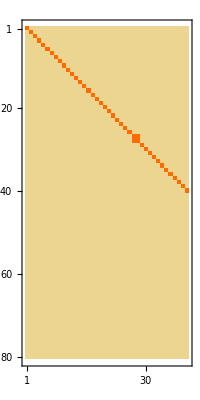
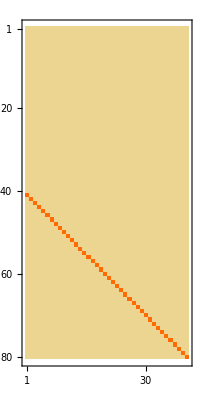

```mathematica
Table[lang/.WMMs//MatrixPlot,{lang,EntityLanguages}]
```

### Graph Data Initialization

#### > Vertex and Edge Properties > Viz initial Graph

```mathematica
VocabDist[l0_,l1_]:=Module[
{i},
Return[Mean[Table[EditDistance[(l0/.LanguageVocabs)[[i]],(l1/.LanguageVocabs)[[i]]],{i,MeaningCount}]]]]
```

```mathematica
lookupIPACost[s_,t_]:= Module[{acceptedSymbols}, acceptedSymbols = {"b","β","d","ð","f","g","ɣ","ʝ","ɟ","k","l","ʎ","m","ɱ","n","ɲ","ŋ","p","r","ɾ","s","θ","t","v","x","z","a","e","i","o","u","j","w","ʃ","h","ʒ","ɑ","ɒ","æ","ɪ","ɛ","ɔ","ʊ","ʌ","ə","ʋ","ø","y","ʂ","ʐ","ʑ","ɕ","ɨ","ɵ","ʉ","ɐ","ç","ʁ","ɹ","c","q","ɜ","ɡ","ɦ","ʏ"};
If[ContainsAll[acceptedSymbols, {s,t}],Return[Part[ipaConfusionMatrix, Part[Position[acceptedSymbols, s],1,1],Part[Position[acceptedSymbols, t],1,1] ]], Return[1]]
]
```

```mathematica
PhoneticDiff[s_,t_]:=Module[{d, cost},d=ConstantArray[0,{StringLength[s]+1,StringLength[t]+1}]//MatrixForm;
For[i=1,i<StringLength[t]+1,i++,Part[d,1,1,i+1]=i];
For[i=1,i<StringLength[s]+1,i++,Part[d,1,i+1,1]=i];
For[j=2,j<=StringLength[t]+1,j++,
For[i=2,i<=StringLength[s]+1,i++,
If[StringTake[s,{i-1}]==StringTake[t,{j-1}],cost=0,cost=lookupIPACost[StringTake[s,{i-1}],StringTake[t,{j-1}]]];
Part[d,1,i,j]=Min[Part[d,1,i-1,j]+cost,Part[d,1,i,j-1]+cost,Part[d,1,i-1,j-1]+cost];]];
Return[Part[d,1,StringLength[s]+1,StringLength[t]+1]]]
```

```mathematica
PhoneticDist[l0_,l1_]:=Module[{i},
Return[Mean[Table[PhoneticDiff[(l0/.PhoneticVocab)[[i]],(l1/.PhoneticVocab)[[i]]],{i,MeaningCount}]]]]
```

```mathematica
EdgeWeightFunction[l0_,l1_]:=Module[
{AlphabetDiff=EditDistance[Alphabet[l0],Alphabet[l1]],
LevenDist=VocabDist[l0,l1],
PhoneticDist = PhoneticDist[l0,l1]},
Return[If[l0["Name"]==l1["Name"],Infinity,Rescale[N[AlphabetDiff+LevenDist+PhoneticDist],{0,50}]]]]
```

```mathematica
WAM=Module[{i,j},
Table[EdgeWeightFunction[i,j],{i,EntityLanguages},{j,EntityLanguages}]]; MatrixForm[WAM]
```

(∞ | 0.8413
0.8413 | ∞)

```mathematica
Graph0=WeightedAdjacencyGraph[EntityLanguages,WAM];
```

```mathematica
LanguageSizes=Length@#["OfficialSpeakingCountries"]&/@EntityLanguages
```

{1,5}

```mathematica
EdgeWeights=(DeleteDuplicates@*Flatten@WAM)[[2;;]]
```

{0.8413}

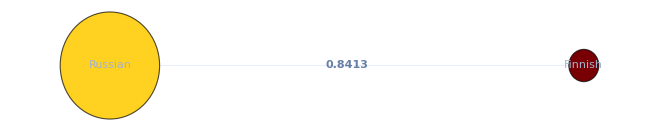

```mathematica
g1=SetProperty[Graph0,{
VertexLabels->Placed["Name",Center],
VertexLabelStyle->Directive[Larger],
VertexWeight->LanguageSizes,
VertexSize->Thread[VertexList[Graph0]->.2 N[.1+Rescale[LanguageSizes]]^.5],VertexStyle->Thread[VertexList[Graph0]->(ColorData["SolarColors"]/@Rescale[LanguageSizes])],
EdgeLabels->Placed["EdgeWeight", Center],
EdgeLabelStyle->Directive[Bold,Larger],
EdgeStyle->Thread[EdgeList[Graph0]->(Directive[Thickness[#/100],ColorData["TemperatureMap"][#]]&/@Rescale[EdgeWeights])]}]
```

### Game and Interacting Functions

#### > Get Graph data for functions > Update[Word/Meaning] functions > Utilities Functions

```mathematica
UpdateWord[word_,lambda_,meaningid_,gameWon_]:=Module[{
correctMeaningProb=word[[meaningid]],
sign=If[gameWon,1,-1],
n=Length[word]
},
Return[RescaleRow[Table[
If[eachmeaning!=meaningid,
newMeaning=word[[eachmeaning]]-Divide[sign*lambda,n-1];
If[newMeaning<0,0,If[newMeaning>1,1,newMeaning]],
newMeaning=correctMeaningProb+sign*lambda;
If[newMeaning>1,1,If[newMeaning<0,0,newMeaning]]],
{eachmeaning,1,Length[word]}]]]
]
```

```mathematica
UpdateMeaning[meaning_,lambda_,wordid_,gameWon_]:=Module[{
correctWord=meaning[[wordid]],
sign=If[gameWon,1,-1],
n=Length[meaning]
},
Return[Table[If[eachword!=wordid,
newword=meaning[[eachword]]-Divide[sign*lambda,n-1];
If[newword<0,0,If[newword>1,1,newword]],
newword=correctWord+sign*lambda;
If[newword>1,1,If[newword<0,0,newword]]],
{eachword,1,Length[meaning]}]]
]
```

```mathematica
UpdateWeight[l0_,l1_,lambda_]:=Module[{
oldweight=PropertyValue[{Graph0,l0<->l1},EdgeWeight],
l0id=Position[EntityLanguages,l0],
l1id=Position[EntityLanguages,l1]
},
newweight=(lambda/2)+(oldweight/2);
Return[If[newweight>1,1,newweight]]
]
```

```mathematica
UpdateGraphData[graph_]:=Block[{g=graph},
Print["TODO:UPDATE GRAPH DATA (VERTEX COORDS & WEIGHTS"]]
```

```mathematica
RescaleRow[row_]:=row/Total[row]
```

### Loops

#### > Game Loop > Graph interaction Loop

For each game loop, given two languages L0(Speaker) and L1(Listener): 
	- Softmax each row for both languages. 
	- SpokenWord := RandomChoice a word for a random meaning in L0.
	- InterpretedMeaning := RandomChoice a meaning for the word in L1.
	- If SpokenWord==InterpretedMeaning -> game won, else -> game lost
	- Update L0 Word and L1 Meaning

```mathematica
RefinementThreshold=.7;
```

```mathematica
GamesTally=ConstantArray[{0,0,0},EntityLanguages//Length]; (*{GamesWon as Speaker, GamesWon as Listener, GamesPlayed}*)
```

```mathematica
PlayNormalGame[L0_,L1_]:=Block[{
SpeakerWMM = L0 /. WMMs,
ListenerWMM=L1/.WMMs,
GameMeaningID=RandomInteger[{1,MeaningCount}],
Lambda=1-Max[PropertyValue[{Graph0,L0<->L1},EdgeWeight],PropertyValue[{Graph0,L1<->L0},EdgeWeight]]
},
GameMeaning=SpeakerWMM[[All,GameMeaningID]];
If[Total[GameMeaning]==0,GameMeaning=ConstantArray[1/MeaningCount,WordsCount]];
SpokenWordID=RandomChoice[GameMeaning->Range[WordsCount]];
InterpretedMeaningID=RandomChoice[ListenerWMM[[SpokenWordID]]->Range[MeaningCount]];
SpeakerCorrect= Flatten[Position[L0 /.LanguageVocabs,AllWords[[SpokenWordID]]]]=={GameMeaningID};
ListenerCorrect=InterpretedMeaningID==GameMeaningID;
GameWon=SpeakerCorrect&&ListenerCorrect ;

(*Print[StringForm["`` => L0: `` => L1: `` |==> ``... Updating `` by ``",UniversalMeanings[[GameMeaningID]],AllWords[[SpokenWordID]], UniversalMeanings[[InterpretedMeaningID]], GameWon, If[GameWon, {{"s", L0},{"l",L1}}, If[SpeakerCorrect,{"l",L1},If[ListenerCorrect,{"s",L0}, "none"]]],Lambda]];*)

If[SpeakerCorrect,
ListenerWMM[[SpokenWordID]]=UpdateWord[ListenerWMM[[SpokenWordID]],Lambda,InterpretedMeaningID,GameWon]];
If[ListenerCorrect,
SpeakerWMM[[All,GameMeaningID]]=UpdateMeaning[SpeakerWMM[[All,GameMeaningID]],Lambda,SpokenWordID,GameWon];
SpeakerWMM=Table[RescaleRow[row],{row,SpeakerWMM}]];

WMMs = WMMs/.{(L0->_):>L0->SpeakerWMM, (L1->_):>L1->ListenerWMM};
AppendTo[AllWMMs,WMMs];
Return[GameWon]
];
PlayTeacherGame[L0_,L1_]:=Block[{
TeacherWMM = L0 /. WMMs,
StudentWMM=L1/.WMMs,
GameMeaningID=RandomInteger[{1,MeaningCount}],
L0WordMaxRange=Flatten[Position[EntityLanguages,L0]][[1]]*40,
Lambda=1-Max[PropertyValue[{Graph0,L0<->L1},EdgeWeight],PropertyValue[{Graph0,L1<->L0},EdgeWeight]]
},
GameMeaning=TeacherWMM[[All,GameMeaningID]];
If[Total[GameMeaning]==0,GameMeaning=ConstantArray[1/MeaningCount,WordsCount]];
SpokenWordID=RandomChoice[Take[GameMeaning,{L0WordMaxRange-39,L0WordMaxRange}]->Range[L0WordMaxRange-39,L0WordMaxRange]];

(*Print[StringForm["`` => L0: `` => L1: `` |==> ``... Updating `` by ``",UniversalMeanings[[GameMeaningID]],AllWords[[SpokenWordID]], UniversalMeanings[[InterpretedMeaningID]], GameWon, If[GameWon, {{"s", L0},{"l",L1}}, If[SpeakerCorrect,{"l",L1},If[ListenerCorrect,{"s",L0}, "none"]]],Lambda]];*)

StudentWMM[[SpokenWordID]]=UpdateWord[StudentWMM[[SpokenWordID]],Lambda,GameMeaningID,True];
TeacherWMM[[All,GameMeaningID]]=UpdateMeaning[TeacherWMM[[All,GameMeaningID]],Lambda,SpokenWordID,True];
TeacherWMM=Table[RescaleRow[row],{row,TeacherWMM}];

WMMs = WMMs/.{(L0->_):>L0->TeacherWMM, (L1->_):>L1->StudentWMM};
Return[True]
];
```

```mathematica
CommonLanguageFound:=((Equivalent@@Table[Flatten[Position[row,Max[row]]],{lang,EntityLanguages},{row,lang/.WMMs}])//TautologyQ)&& (And@@(Table[Max[row]>=RefinementThreshold,{lang,EntityLanguages},{row,lang/.WMMs}]//Flatten))
```

```mathematica
GameIterations[GameTypeDistribution_]:=Module[{
GameToPlay:=RandomChoice[GameTypeDistribution->{PlayNormalGame,PlayTeacherGame}],
speaker,
listener,
i},
i=0;
While[!CommonLanguageFound,
{speaker,listener}=RandomSample[EntityLanguages,2];
If[GameToPlay[speaker,listener],
GamesTally[[Position[EntityLanguages,speaker]//Flatten,1]]++;
GamesTally[[Position[EntityLanguages,listener]//Flatten,2]]++];
GamesTally[[Position[EntityLanguages,speaker]//Flatten,3]]++;
GamesTally[[Position[EntityLanguages,listener]//Flatten,3]]++;
If[i>=600,Print["ran over max iterations... breaking loop"];Break[],i++]
];
]
```

```mathematica
AbsoluteTiming[GameIterations[{.8,.2}]]
```

ran over max iterations... breaking loop

{1.79931,Null}

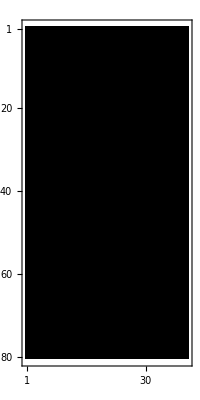
{-Graphics-,-Graphics-}

```mathematica
Table[MatrixPlot[u/.InitialWMMs,PlotTheme->"Monochrome"],{u,EntityLanguages}]
```

```mathematica
Table[MatrixPlot[u/.WMMs,PlotTheme->"Monochrome"],{u,EntityLanguages}]
```

{-Graphics-,-Graphics-}

```mathematica
Animate[Table[lang/.AllWMMs[[u]]//MatrixPlot,{lang,EntityLanguages}],{u,1,Length[AllWMMs],1}]
```

```mathematica
Ceiling[#/40]&/@((#[[1]])&/@Table[Position[meaning,TakeLargest[meaning,2][[2]]]//Flatten,{meaning,(EntityLanguages[[2]]/.WMMs)ᵀ}])/.Thread[Range[EntityLanguages//Length]->EntityLanguages]//Tally
```

{{Finnish,38},{Russian,2}}